```mathematica
Needs["MazeNavigation`"]
Needs["VisualizeGenome`"]
```

## Create Map

```mathematica
map1=Rasterize[Graphics[{Antialiasing->False,Black,Thickness[0.05],Line[{{1,1},{20,1},{20,20},{1,20},{1,1}}],
Line[{{1,5},{20,10}}],
Line[{{1,6},{20,11}}]
}],RasterSize->{20,20}];
map1=(map1/.Graphics->List)[[1,1]]/.{{0,0,0}->1,{255,255,255}->0};
map1[[4,2]]=2;
map1[[15,15]]=3;
```

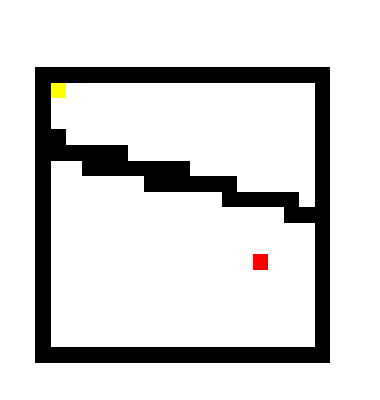

```mathematica
ArrayPlot[map1,ColorRules->{0->White,1->Black,2->Yellow,3->Red}]
```

```mathematica
Export["map1.csv",map1]
```

map1.csv

## Player

```mathematica
data=readAllFiles[{"GPAT_MAZE_MAP4_ORIG"}];
printAsTable[data,{"SOLVER"}]
expr=convertGPATGenome[sortConfigurationResults[data,"1","BSF",10,Output->"BSF"][[1,4]]]
```

ID | PARAM FILE | SOLVER
1 | GPAT_MAZE_MAP4_ORIG/parameters_001.txt | GPAT

{-ArcTan[3.10957+0.472039 x0-6.8829 x1+2.8946 x2-2.24012 x3+1.61314 x4+0.749032 x5-1.81171 x6]}

```mathematica
expr={Plus[-0.6469302754514258*x5]}
```

{-0.64693 x5}

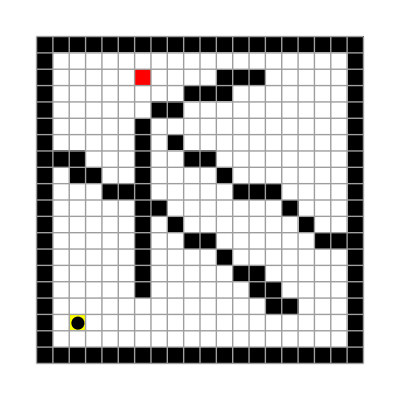

```mathematica
(state=loadMap["~/java/ne/cfg/demo/maze/map4.csv"])//showState
```

```mathematica
Manipulate[Nest[singleStep[#,expr]&,state,i]//showState,{i,0,100,1}]
```

```mathematica
data2=readAllFiles[{"GPAT_MAZE_MAP4_ORIG"}];
bestN=1;(*n-th best run*)
state2=loadMap["~/java/ne/cfg/demo/maze/map4.csv"];
printAsTable[data2,{"SOLVER"}]
expr2=
listBSFEvolution[Sequence@@(sortConfigurationResults[data2,"1","BSF",bestN,Output->"GenomeFileList"][[bestN]]),Choice->"Changing"];
Print[expr2//MatrixForm];
expr2=convertGPATGenome[expr2];
```

ID | PARAM FILE | SOLVER
1 | GPAT_MAZE_MAP4_ORIG/parameters_001.txt | GPAT

(1 | 16 | -1 | {plus} | 20.
2 | 153 | 16 | {plus[1.01262 x2]} | 30.
4 | 318 | 224 | {plus[-4.75473 x2,1. x4]} | 30.
5 | 488 | 318 | {plus[-4.75473 x2,1.31942 x4,1. x0]} | 27.
8 | 765 | 675 | {atan[x2,x4,x5]} | 29.
9 | 859 | 765 | {atan[x2,x4,x4,x4]} | 30.
39 | 3835 | 3731 | {atan[x2,x4,x4,x4,x3]} | 21.
40 | 4000 | 3835 | {gauss[x2,x4,x4,x4,x3,x6]} | 20.
46 | 4561 | 4473 | {plus[2.96311 x2,-3.84804 x4,-0.966561 x4,0.829588 x4,1. x3,0.998676 x6]} | 23.
48 | 4762 | 4681 | {sin[plus[2.96311 x2,-3.84804 x4,-0.966561 x5,0.829588 x4,-4.99094 x3,0.998676 x6]]} | 30.
76 | 7523 | 7410 | {sin[plus[2.96311 x2,-3.84804 x4,-4.388,2.09366 x4,-0.236861 x3,1.02686 x6,0.991656 x0]]} | 27.
77 | 7697 | 7523 | {sin[plus[2.96311 x2,-3.84804 x4,-4.37732,2.09366 x4,-0.236861 x3,-4.3994 x6,0.991656 x0]]} | 29.
78 | 7787 | 7697 | {sin[plus[2.96311 x2,-3.83774 x4,-4.37732,-4.33952 x1,-0.236861 x3,-4.40048 x6,0.991656 x0]]} | 31.
215 | 21493 | 21377 | {sin[plus[2.96311 x2,-3.83774 x4,-4.36636,-0.678289 x1,-0.236861 x3,-4.39403 x6,0.991656 x0],x1]} | 31.
240 | 23968 | 23873 | {sin[plus[2.96311 x2,-0.981241 x4,1.28005 x5,-0.678289 x1,-0.236861 x3,-4.39403 x6,0.991656 x0],x1]} | 33.
517 | 51649 | 51529 | {sin[plus[2.95516 x2,-0.981241 x4,1.28005 x5,-0.677439 x1,-0.236861 x3,-4.39403,0.991656 x0],x1]} | 19.
518 | 51800 | 51649 | {sin[plus[2.95516 x2,-0.983355 x4,4.50412 x5,-0.294442 x1,-0.186711 x3,-4.38838,0.991656 x0],x1,x2]} | 30.
523 | 52256 | 52180 | {sin[plus[2.95696 x2,-0.981424 x4,4.71262 x5,-0.294442 x1,-0.186711 x3,-4.38838,0.935933 x0],x1,x4]} | 33.
568 | 56793 | 56696 | {sin[plus[2.95696 x2,-0.984333 x4,4.71262 x5,0.411852 x1,-0.186711 x3,-4.38838,0.935933 x0],x1,x4,x5]} | 29.
571 | 57088 | 56982 | {atan[plus[2.95696 x2,-2.57701 x4,-3.22961 x5,0.402033 x1,2.24012 x3,-4.44902,0.935933 x0,1.80427 x6],x1,x4,x5]} | 27.
572 | 57196 | 57088 | {atan[plus[3.08968 x2,-2.57701 x4,-3.22961 x5,0.37421 x1,2.24012 x3,-1.0153,0.949963 x0,1.80427 x6],x1,x4,x5]} | 28.
577 | 57681 | 57582 | {atan[plus[-1.03653 x2,-2.57701 x4,-3.22961 x5,0.37421 x1,2.24012 x3,-1.57401,0.949963 x0,1.8081 x6],x1,x4,x5]} | 30.
578 | 57792 | 57681 | {atan[plus[-2.8946 x2,-2.57063 x4,-0.694471 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x5]} | 38.
638 | 63751 | 63652 | {atan[plus[-2.8946 x2,-2.61314 x4,-0.749032 x5,4.8829 x1,2.24012 x3,-3.10957,-0.472039 x0,1.81171 x6],x1,x4,x1]} | 40.)

```mathematica
{1,14,15,22,24,33,37,38}
```

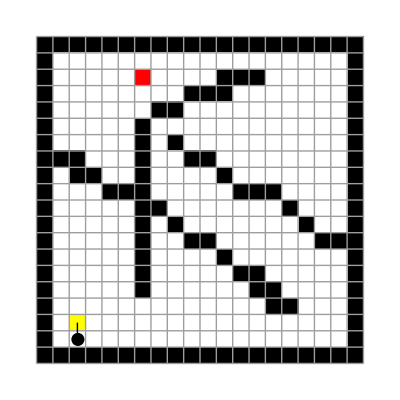
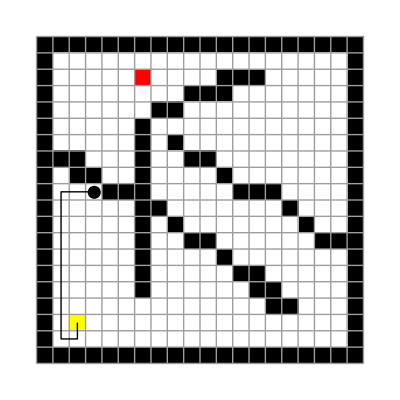
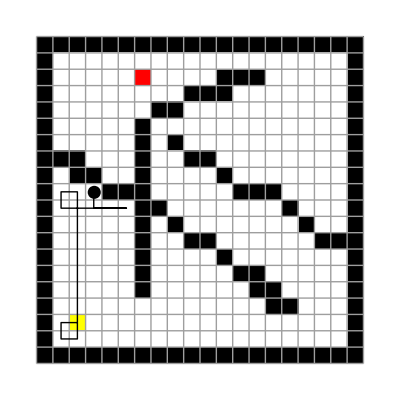
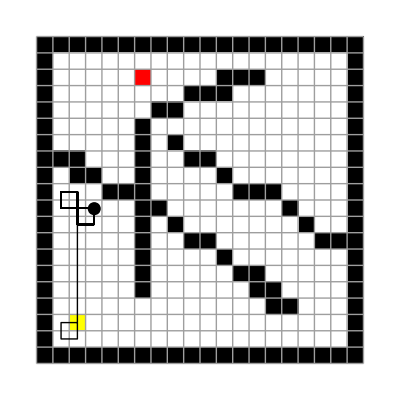
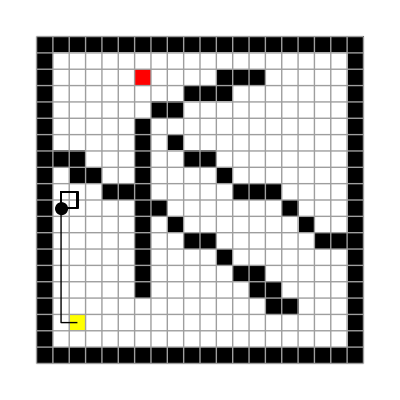
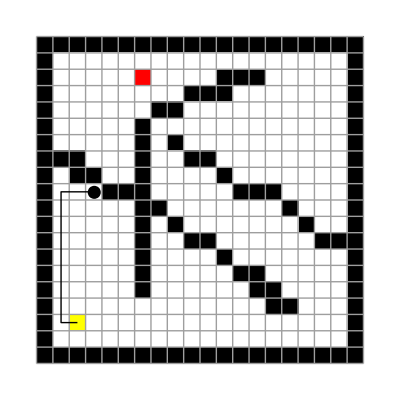
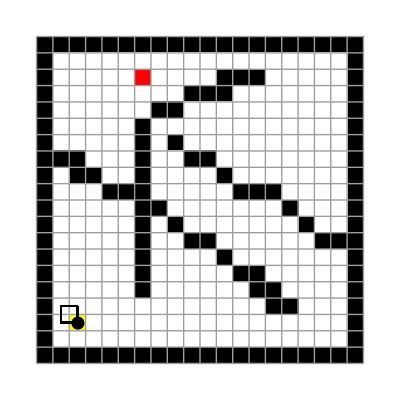
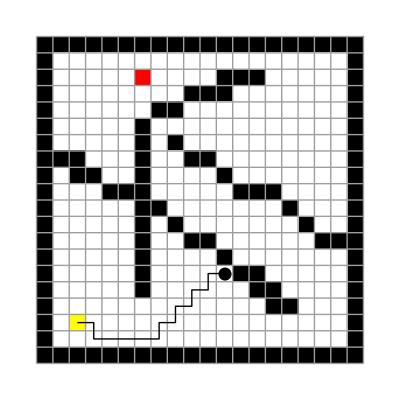
{-Graphics-
Generation 1
f = 20.,-Graphics-
Generation 2
f = 30.,-Graphics-
Generation 4
f = 30.,-Graphics-
Generation 5
f = 27.,-Graphics-
Generation 8
f = 29.,-Graphics-
Generation 9
f = 30.,-Graphics-
Generation 39
f = 21.,-Graphics-
Generation 40
f = 20.,-Graphics-
Generation 46
f = 23.,-Graphics-
Generation 48
f = 30.,-Graphics-
Generation 76
f = 27.,-Graphics-
Generation 77
f = 29.,-Graphics-
Generation 78
f = 31.,-Graphics-
Generation 215
f = 31.,-Graphics-
Generation 240
f = 33.,-Graphics-
Generation 517
f = 19.,-Graphics-
Generation 518
f = 30.,-Graphics-
Generation 523
f = 33.,-Graphics-
Generation 568
f = 29.,-Graphics-
Generation 571
f = 27.,-Graphics-
Generation 572
f = 28.,-Graphics-
Generation 577
f = 30.,-Graphics-
Generation 578
f = 38.,-Graphics-
Generation 638
f = 40.}

```mathematica
grid=Grid[{{simulateToTarget[state2,#[[4]],120]},{"Generation "<>ToString[#[[1]]]}, {Style["f = "<>ToString[#[[5]]],Italic]}}]&/@expr2
```

```mathematica
MapIndexed[Export["110817_visualizeRun_MAP_"<>ToString[Sequence@@#2+11]<>".pdf",#1]&,grid[[{1,14,15,22,24,33,37,38}]]]
```

{110817_visualizeRun_MAP_12.pdf,110817_visualizeRun_MAP_13.pdf,110817_visualizeRun_MAP_14.pdf,110817_visualizeRun_MAP_15.pdf,110817_visualizeRun_MAP_16.pdf,110817_visualizeRun_MAP_17.pdf,110817_visualizeRun_MAP_18.pdf,110817_visualizeRun_MAP_19.pdf}